# AD_Excitation

## 1D ground state

## useful function

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};Load energy[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]][[-2]]
Load Time Step Energy gnorm[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
```

## Heisenberg

#### relative error-χ

error exponentially-dependent on χ

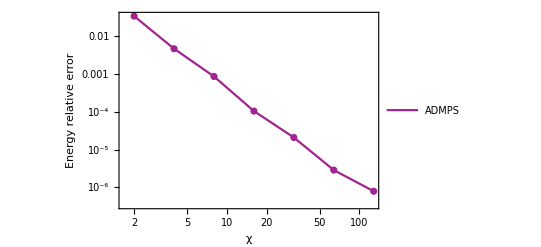

```mathematica
exact=0.25-Log[2];
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
ListLogLogPlot[{AD MPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
```

#### relative error-steps

error exponentially-dependent on steps

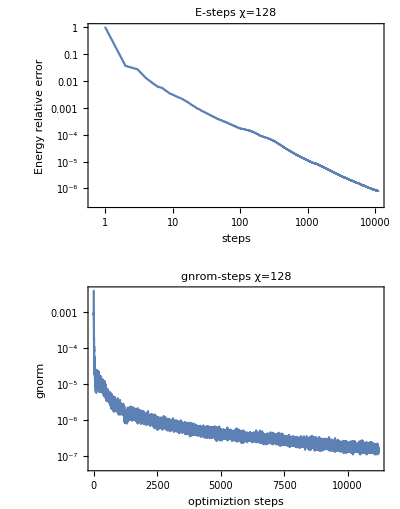

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## TFIsing at critical point g=0.5

#### relative error-χ

error exponentially-dependent on χ

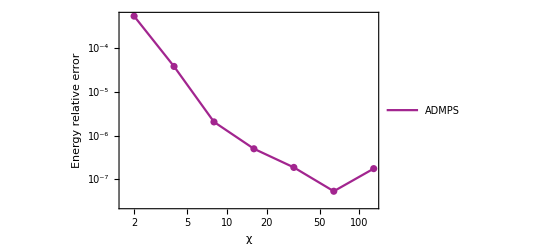

{{2,0.000547469},{4,0.0000384942},{8,2.06229×10^-6},{16,4.99614×10^-7},{32,1.86865×10^-7},{64,5.3171×10^-8},{128,1.75275×10^-7}}

```mathematica
g=1;exact=Integrate[-1/(2Pi)Sqrt[g^2-2g Cos[k]+1],{k,0,2Pi}]/4;
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
ListLogLogPlot[{AD MPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
AD MPS energy aberror
```

#### relative error-steps

error exponentially-dependent on steps

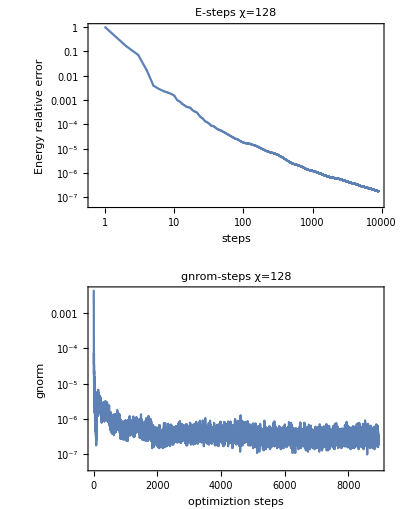

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## 1D Excitation

## U1

```mathematica
U1 = {{0.44214127746903376-0.36649815518214574I,-0.13700868205515632-0.16528649180042596I},{0.1370086836991797+0.1652864904376679I, 0.23346510468812767-0.1935230536660265I}};
U2 = {{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}
```

{{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}

```mathematica
FindRoot[Tr[Transpose[U1].U2]==0,{x,1}]
```

{x→1.5708+0.535137 ⅈ}

```mathematica
U=U2/.{x->1.5707963267948966+0.5351372028447591 ⅈ}
```

{{7.02112×10^-17-0.561047 ⅈ,-1.14664-3.43542×10^-17 ⅈ},{1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17-0.561047 ⅈ}}

```mathematica
FullSimplify[Transpose[U].U]
```

{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
ConjugateTranspose[U]
```

{{7.02112×10^-17+0.561047 ⅈ,1.14664-3.43542×10^-17 ⅈ},{-1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17+0.561047 ⅈ}}

## XXZ Δ=1

```mathematica
0.019355722801703747,0.04098969536943847,0.09555269661385882,0.19834470914903002,0.3307304901940979,0.4771994131300664
```

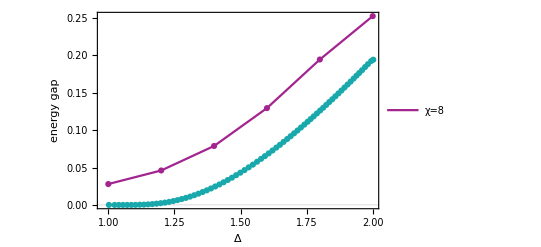

```mathematica
gap={0.05582453026702144,0.09212963838012368,0.15765165546585008,0.25902554676265305,0.38907021917034657,0.5051298373530196}/2;
energy gs=Table[{1.0+0.2(i-1),Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\XXZ{Float64}("<>ToString[NumberForm[1.0+0.2(i-1),{2,1}]]<>")\\D2_χ8.log"]},{i,1,6}];
energy gap=Table[{energy gs[[i,1]],gap[[i]]},{i,1,Length[gap]}];
Exact = Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\project\\XXZ_gap.csv"];
ListPlot[{energy gap,Exact },PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=8"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"Δ",None}},ImageSize->400]
```

## Heisenberg S=1/2

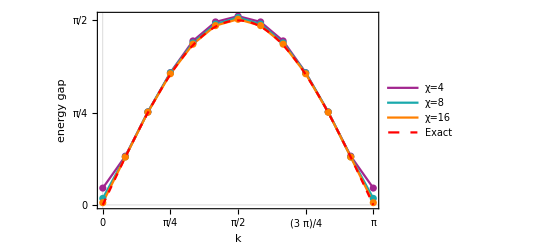

```mathematica
gap={{0.143590951236512,0.41530630963142906,0.7919144836295847,1.1263906176088896,1.3962166412387695,1.5578014262286415,1.6073219940962598,1.5578014252762273,1.3962166412329813,1.1263906186752397,0.791914483411365,0.415306313325118,0.14359095621658013},{0.055825535280367065,0.40920812813787655,0.7917343968681471,1.124766271557226,1.379519702559978,1.5398361831063736,1.5948824096077312,1.5398361216280303,1.3795198076975546,1.1247663680286026,0.791734354199969,0.40920812220705727,0.055826048730513896},{0.019355656610179933,0.40749600807271985,0.7893265909061853,1.116831940068277,1.368569477493216,1.526614821143771,1.5805417601476666,1.5266152002333788,1.3685691333818455,1.116831994201616,0.7893267774108071,0.40749554338175925,0.01936395160433102}};
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,3},{i,1,Length[gap[[1]]]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=4","χ=8","χ=16"},{Scaled[{0.7,0.2}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],Plot[Pi/2Sin[x],{x,0,Pi},PlotLegends->Placed[{"Exact"},{Scaled[{0.6,0.8}], {0, 0}}],PlotStyle->{Dashed,Red},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]}]]
```

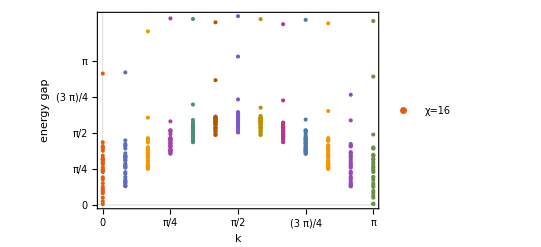

```mathematica
data={{0.019356712019114892,0.07988399537000476,0.15851980030219873,0.25463892314106706,0.287120756397108,0.30459423982442213,0.3479629943878291,0.3922590290112449,0.4730370929326074,0.5577705457747633,0.6004789242641874,0.718590070430259,0.7439289900867999,0.7495836084115252,0.7821209734141411,0.8229444507585456,0.8971681651337648,0.901995097855716,0.9439744124606408,0.9696428965384598,0.9958241788054643,1.0041003694226043,1.0054805948271819,1.0745533155732234,1.180929290460144,1.2325044004821992,1.2532894962360224,1.2837474621301057,1.3667881667284276,2.8646066019201752,},{0.40749545997731024,0.4142511021698713,0.43356413933476184,0.475406537485462,0.49283245623109206,0.5028117913747882,0.5287702964271762,0.5571428958544163,0.6106206879634741,0.6803569308483806,0.714178426296922,0.8115120209843482,0.8356798773101553,0.8374586977078984,0.8699178607399839,0.9019830647090546,0.9712917165007591,0.9737498932970463,1.0115021472245342,1.0364849155901132,1.055766434877827,1.0687115459542742,1.068754854037054,1.1253272036295503,1.2306250163019161,1.2817346376112082,1.3021807343637686,1.3300632810400672,1.4075640707087964,2.8889855941756273,},{0.7893266944597348,0.7942501629158961,0.8080983901196898,0.8329832624770432,0.8371042143663318,0.8485798469746656,0.8607240204576377,0.8770320060315122,0.8965651986306411,0.9528899687030133,0.97344525072165,1.0335063173750503,1.0485824510180348,1.0591232417233063,1.085525173213311,1.0985179256179807,1.1558025583204596,1.1603245206639765,1.1890467276198426,1.210974787432773,1.2127473679440022,1.2341645845777038,1.238221476027026,1.2593986762292515,1.3637136820530713,1.4147349287917201,1.4351944870496096,1.455853661606546,1.9035620925279053,3.7848677083057747,},{1.116831502605037,1.12476530849907,1.15430460646794,1.1687978477015146,1.1799055417539226,1.193694864650017,1.2010668235112858,1.201140538762355,1.2091965592227063,1.2590291983596569,1.2695786907497852,1.2892016469960854,1.293902273245662,1.3274472663598187,1.3388464110793226,1.351369027978242,1.3802791573229731,1.3931407515569652,1.4233732296129213,1.4258267355362826,1.4319920587187818,1.4419554188371382,1.4510467492380943,1.4647142285637693,1.5417525377787744,1.5971300132545627,1.620147193335427,1.6285552425540075,1.8219652516480467,4.066599204359205,},{1.3685689761889452,1.376751307097338,1.417512024110783,1.4435360358612712,1.4655676725300586,1.4894342455817675,1.4964296394145618,1.4989335515925373,1.5005635828143817,1.529068157428938,1.540174901301829,1.5487475185851236,1.549745216104134,1.568148444458624,1.5951481865176167,1.6000923532044522,1.6027327280920682,1.6164856580165312,1.6169190387860428,1.6699323819821772,1.6731677946889956,1.678444718734378,1.6849843360854513,1.7034394313919503,1.7217408643561687,1.763768502785001,1.7960796086984125,1.8504555137484338,2.190241957087645,4.055459789874986,},{1.5266146074808955,1.5351495579404821,1.5852007179262673,1.6093648946563477,1.636486546352942,1.6681632428651025,1.6823737812163686,1.6844391306143944,1.6847106624278922,1.7385630207524074,1.759565796077722,1.762173773125544,1.7701121016717183,1.7983222443292795,1.8105773125905387,1.8126719689438504,1.8155815421714279,1.8327868545942116,1.8381796981024656,1.8615650039854224,1.8678147252962165,1.8779402568886399,1.8924265833368583,1.8939565537326823,1.8943462671356877,1.905613231280845,1.9090383533701487,1.9254452214636193,2.72055401273043,3.9819833812412218,},{1.5805411732081112,1.5886593033410528,1.641749100020726,1.665547988944231,1.6991894622430865,1.7327092534729733,1.743381215790137,1.7497299643816298,1.7512167174567566,1.7918517854271931,1.8197636782730775,1.8212953766296298,1.825514991333764,1.8725561523658738,1.8909546742403205,1.8951320551583912,1.9045335366632057,1.9117764622737465,1.920216706315951,1.9711582067056597,1.9810155992977627,1.9947806931276375,1.9962842709797617,1.9965842909499656,2.0106626043637825,2.010819084407383,2.02378002915089,2.3005953636131786,3.235245494623999,4.116815393592645,},{1.5266146138295849,1.5337556104531076,1.585200740724084,1.6038439808725744,1.6364865104873207,1.6681635510681518,1.6823743144080967,1.6844387184175804,1.6929936377195653,1.730416462551267,1.7597857149708078,1.762173721632632,1.7701122211897062,1.7983223863939903,1.8105776141303231,1.8126718024052313,1.821274003365932,1.8327869465416147,1.8381795434754769,1.8440545833225725,1.8668261790832716,1.8779400494286325,1.8800024063408864,1.8924270460964727,1.8939575179101493,1.9056128515933148,1.9090378879259335,1.93987840005778,2.120094532159012,4.051593416680396,},{1.3685689764707742,1.3740018027016563,1.4175120848230747,1.4341878776695516,1.4655678198986097,1.489434552371823,1.4964299453534982,1.5005633268494591,1.5065077555628699,1.5135155761110382,1.5401749811009575,1.5483409819989356,1.548747165873286,1.5681498852450781,1.5951490487159559,1.6027322561778543,1.6156936862333289,1.6164862103488604,1.61691878927919,1.6633651250986146,1.6699333721222533,1.6784439961118993,1.703438341852252,1.7106140402687966,1.7136607038689378,1.7637669518331391,1.779810296957471,1.7960831218801239,2.278523198771948,3.9406181549128902,},{1.1168315115650753,1.1207256917563961,1.1543046308875105,1.160738320405532,1.1799055623809236,1.1936950195808922,1.2011408221233486,1.2091967975413735,1.2153399744747992,1.2466981314308494,1.2574855989210585,1.269577526050929,1.2892022380823884,1.327449384795426,1.3388470200992217,1.351368767498939,1.3721818850663645,1.3931413016927126,1.42337462783548,1.4258258587337995,1.4319929567168939,1.4646458055137497,1.4647136636986695,1.5074935543002541,1.5528414394724142,1.5971359155909663,1.6201469299457782,1.6285599198032636,1.8610595953487552,4.035370165640145,},{0.7893266963883178,0.7913374803738014,0.80809848355993,0.8154143044684896,0.8329832684142604,0.8485804862629531,0.8770323231891377,0.8917846288044309,0.8965655139162783,0.9466469949855978,0.9719074984729527,0.9734429173911155,1.0335067709653576,1.059123422951192,1.0855250948258277,1.0985209435743524,1.1220578572457651,1.160324874589181,1.1890460611067981,1.212751030826172,1.2382221841192163,1.2593986095342762,1.2739426924891868,1.3025837838412864,1.3957009117589567,1.4147438170082063,1.4351942444313903,1.4558556418346649,2.0483544183513422,3.9593347538821706,},{0.40749546536827774,0.40832868355849616,0.4335642927414416,0.44972609512798917,0.4754064545027773,0.5028128058092911,0.5571433015687848,0.5838917988115573,0.6106208674872218,0.6707863030727833,0.7141743390620788,0.7228397998790248,0.8115122447729578,0.8356807001116999,0.8699179445069521,0.9019865286637174,0.9212591100229373,0.9712921208859898,1.0115017943993811,1.055770828421495,1.0687574401044815,1.1253270284754826,1.1283875952837439,1.1503946181792346,1.2768589231067016,1.2817457004444024,1.3021805897405276,1.3300656037606284,1.8439581798161688,2.402502242249594,},{0.019356809950179597,0.029916300562974875,0.1585200675923619,0.1981441049937934,0.2546389233505662,0.30459575025163155,0.39225940990771535,0.43130061036785206,0.47303709405531175,0.5453999132929324,0.6004734606841438,0.6122869967014534,0.7185900761089724,0.7439301071199007,0.7821209792088036,0.8229479832735931,0.8412597973315288,0.8971684032726289,0.9439744118898505,0.9958274004267408,1.0041054365803053,1.0732846893904768,1.0745533266265916,1.0933159940135706,1.2323046279511454,1.2325162441319775,1.253289496260357,1.5347002921036776,2.7990200297345713,4.010786579441088,}};
energy gap=Table[Transpose@{Table[Pi/12 (i-1),{j,1,Length[data[[i]]]}],data[[i]]},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,PlotStyle->{},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=16"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

## Heisenberg S=1

```mathematica
0.41044325538479737
```

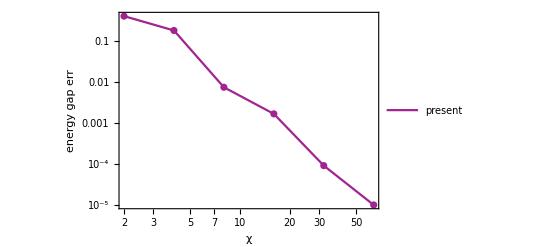

```mathematica
gap={0.5811172937623585,0.4864179655123887,0.40739832778964274,0.40979313525841843,0.41044228122259074,0.410475228123841};
Verstraete2012=0.410479248463;
energy gap=Table[{2^i,Abs[(gap[[i]]-Verstraete2012)/Verstraete2012]},{i,1,Length[gap]}];
Show[ListLogLogPlot[{energy gap},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"present","Verstraete2012"},{Scaled[{0.6,0.5}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap err",None},{"χ",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],PlotRange->All]
```